```mathematica
(* Priklad 1 *)
ClearAll["Global`*"]
ulf = 12. + 7ⅉ;
√(12^2+7^2)
Abs[ulf]
u1[t_]:= Abs[ulf] + Sin[ω*t*Arg[ulf]]
```

√193

13.8924

```mathematica
(* Priklad 2 *)
ClearAll["Global`*"]
um = 15.;
ϕ = π/3;
ulf = um *E^(ⅈ*ϕ)
```

7.5+12.9904 ⅈ

```mathematica
(* Priklad 3 *)
ClearAll["Global`*"]
uf = 9.2 * E^(ⅈ*2.4)
ω = 100
```

-6.78402+6.21426 ⅈ

100

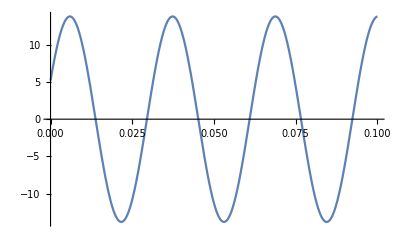

```mathematica
(* Priklad 4 *)
ClearAll["Global`*"]
uf =12.8 + 5.2 ⅉ;
ω = 200;
tmax = 0.1;
u[t_]:= Abs[uf]*Sin[ω*t+Arg[uf]]
Plot[u[t],{t,0,tmax}]
```

{{iu→-0.0000164936-0.000106342 ⅈ,ir→0.0000164936+0.000106342 ⅈ,ic→0.0000164936+0.000106342 ⅈ,u1→3.3+0. ⅈ,u2→3.22248-0.499807 ⅈ}}

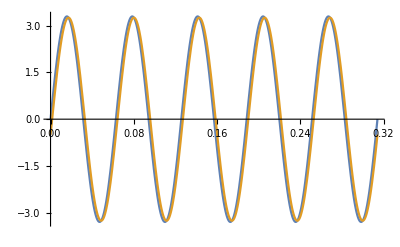

-(0.+644.745 ⅈ)/((0.-644.745 ⅈ)+1. ω)

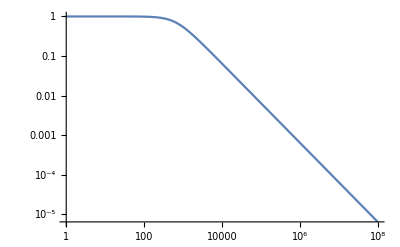

```mathematica
(* Priklad 5 *)
ClearAll["Global`*"]
rovnice = {
(* Uzly *)
0 == iu + ir,
ir == ic,
(* Soucastky *)
uz == u1,
u1 - u2 == r * ir,
u2 == zc * ic
};
soucastky = {
r -> 4700,
c -> 330*10^-9,
zc -> 1/(ⅉ*ω*c),
uz -> 3.3*E^(ⅉ*0)
};
nezname = {iu, ir, ic, u1, u2};
f = 100/(2*π);
tmax = 5/f;
res = Solve[rovnice //.soucastky /.ω -> 100, nezname]
Plot[{Im[u1*E^(ⅉ*ω*t)], Im[u2*E^(ⅉ*ω*t)]} /.res /.ω-> 100 // Evaluate, {t,0,tmax}]
res = Solve[rovnice//.soucastky ,nezname][[1]];
A = u2/u1/. res
LogLogPlot[Abs[A],{ω,1,10^8}, PlotRange -> All]
```

{iu,il,ic,ir,u1,u2}

{iu→((0.+13.2 ⅈ) ((0.-83.3333 ⅈ)+(1.+0. ⅈ) ω))/(-400000.-(0.+83.3333 ⅈ) ω+1. ω^2),il→-((13.2+0. ⅈ) ((83.3333+0. ⅈ)+(0.+1. ⅈ) ω))/(-400000.-(0.+83.3333 ⅈ) ω+1. ω^2),ic→-((0.+13.2 ⅈ) ω)/((-400000.+0. ⅈ)-(0.+83.3333 ⅈ) ω+(1.+0. ⅈ) ω^2),ir→-1100./(-400000.-(0.+83.3333 ⅈ) ω+1. ω^2),u1→3.3,u2→-(1.32×10^6)/(-400000.-(0.+83.3333 ⅈ) ω+1. ω^2)}

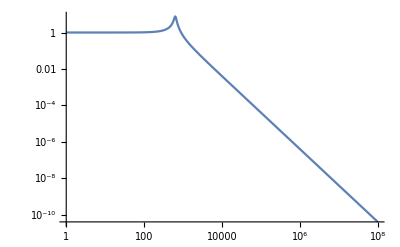

```mathematica
(* Priklad 9 *)
ClearAll["Global`*"]
rovnice ={
(* Uzly *)
0 == iu + il,
il == ic +ir,
(* Soucastky *)
uz == u1,
u1 - u2 == zl * il,
u2 == zc * ic, 
u2 == r *ir
};
soucastky = {
r -> 1200,
l -> 0.25,
c -> 10*10^-6,
zl ->  ⅉ*ω*l,
zc -> 1/(ⅉ*ω*c),
uz -> 3.3
};
nezname = {iu, il, ic, ir, u1,u2}
res = Solve[rovnice //.soucastky, nezname][[1]]
LogLogPlot[Abs[u2/u1/.res], {ω,1,10^8}]
```

```mathematica
(* Priklad 15 *)
ClearAll["Global`*"]
u1 = 10 + 5.6 ⅉ;
u2 = 0.1 + 0.03ⅉ;
A = u2/u1
Abs[A]
```

0.0088916-0.00197929 ⅈ

0.00910923

```mathematica
(* Priklad 16 *)
ClearAll["Global`*"]
u1 = 10 + 5.6 ⅉ;
il = 0.1 + 0.03ⅉ;
z = u1/il
```

107.156+23.8532 ⅈ

```mathematica
(* Priklad 17 je za domaci ukol *)
```